```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ScalingFactor = 0.2;
```

```mathematica
PFunc[a_, u_]:=  1+a*ScalingFactor*Cos[2u+Pi/2]+a*ScalingFactor*Cos[5u+Pi/2]+a*ScalingFactor*Cos[3u]+a*ScalingFactor*Cos[7u+Pi]+a*ScalingFactor/2*Cos[11u];
```

```mathematica
XFunc[a_,u_] := PFunc[a,u]*Cos[u];
YFunc[a_,u_] := PFunc[a,u]*Sin[u];
```

```mathematica
NoiseMatrix = Table[Table[Random[],{i,1,100}],{j,1,100}];
```

```mathematica
NoiseImage =Image[NoiseMatrix, ColorSpace->"Grayscale"]
```

-Graphics-

```mathematica
CreateCell[a_,b_]:=Block[{},
Fill=ParametricPlot[{r*XFunc[a,u],r*YFunc[a,u]},{u,0,2*Pi},{r,0,1} ,Mesh->False,Axes->False,Frame->False,PlotStyle->{Opacity[1], Texture[-Graphics-]},TextureCoordinateFunction->({#1,#2}&), MaxRecursion->3, BoundaryStyle->None];
Outline =ParametricPlot[{XFunc[a,u],YFunc[a,u]},{u,0,2*Pi},Axes->False,Frame->False,PlotStyle->Directive[Black,Thickness[0.02]], MaxRecursion->3];
Middle = ParametricPlot[{r*XFunc[a,u],r*YFunc[a,u]},{u,0,2*Pi},{r,0,.6} ,Mesh->False,Axes->False,Frame->False,PlotStyle->{Opacity[1], Texture[Binarize[NoiseImage,b]]},TextureCoordinateFunction->({#1,#2}&), MaxRecursion->3, BoundaryStyle->None];
Blur[Show[Fill,Outline,Middle],3]]
```

```mathematica
HDCoords = Table[Table[{i,j}, {i, 0.2, 0.8,0.2}],{j, 0.1, 0.9,0.2}];
LDCoords = Table[Table[{i,j}, {i, 0.35, 0.65,0.1}],{j, 0.3, 0.7,0.1}];
HDNovelCoords = Table[Table[{i,j}, {i, {0.2, 0.4,0.6, 0.8}}],{j, {0.2, 0.4,0.6, 0.8}}];
LDNovelCoords = Table[Table[{i,j}, {i, {0.35, 0.45,0.55,0.65}}],{j, {0.35, 0.45,0.55,0.65}}];
```

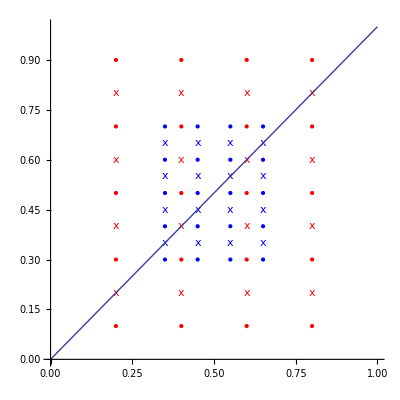

```mathematica
Show[
ListPlot[HDCoords, PlotStyle->Red,PlotRange->{{0,1},{0,1}}, AspectRatio->1],
ListPlot[LDCoords,PlotStyle->Blue],
ListPlot[HDNovelCoords, PlotStyle->Red, PlotMarkers->"x"],
ListPlot[LDNovelCoords, PlotStyle->Blue, PlotMarkers->"x"],
Plot[y=x,{x,0,1}]]
```

```mathematica
StimuliLD = Table[CreateCell[LDCoords[[i]][[j]][[1]],LDCoords[[i]][[j]][[2]]],{i,5,1, -1},{j,1,4}];
```

```mathematica
GraphicsGrid[StimuliLD]
```

-Graphics-

```mathematica
StimuliHD = Table[CreateCell[HDCoords[[i]][[j]][[1]],HDCoords[[i]][[j]][[2]]],{i,1,5},{j,1,4}];
```

```mathematica
GraphicsGrid[StimuliHD]
```

-Graphics-

```mathematica
HDCatACoords=Flatten[HDCoords,1][[{1,2,3,4,5,6,7,9,10,13}]]
```

{{0.2,0.1},{0.4,0.1},{0.6,0.1},{0.8,0.1},{0.2,0.3},{0.4,0.3},{0.6,0.3},{0.2,0.5},{0.4,0.5},{0.2,0.7}}

```mathematica
HDCatBCoords = Flatten[HDCoords,1][[{8,11,12,14,15,16,17,18,19,20}]]
```

{{0.8,0.3},{0.6,0.5},{0.8,0.5},{0.4,0.7},{0.6,0.7},{0.8,0.7},{0.2,0.9},{0.4,0.9},{0.6,0.9},{0.8,0.9}}

```mathematica
HDCatAStims = Table[CreateCell[HDCatACoords[[i]][[1]],HDCatACoords[[i]][[2]]],{i,1,Length[HDCatACoords]}];
HDCatBStims = Table[CreateCell[HDCatBCoords[[i]][[1]],HDCatBCoords[[i]][[2]]],{i,1,Length[HDCatBCoords]}];
```

```mathematica
GraphicsRow[HDCatAStims]
GraphicsRow[HDCatBStims]
```

-Graphics-

-Graphics-

```mathematica
LDCatACoords=Flatten[LDCoords,1][[{1,2,3,4,5,6,7,9,10,13}]];
```

```mathematica
LDCatBCoords = Flatten[LDCoords,1][[{8,11,12,14,15,16,17,18,19,20}]];
```

```mathematica
LDCatAStims = Table[CreateCell[LDCatACoords[[i]][[1]],LDCatACoords[[i]][[2]]],{i,1,Length[LDCatACoords]}];
LDCatBStims = Table[CreateCell[LDCatBCoords[[i]][[1]],LDCatBCoords[[i]][[2]]],{i,1,Length[LDCatBCoords]}];
```

```mathematica
GraphicsRow[LDCatAStims]
GraphicsRow[LDCatBStims]
```

-Graphics-

-Graphics-

```mathematica
HDCatANovelCoords = Flatten[HDNovelCoords,1][[{1,2,3,4,5,7}]];
HDCatBNovelCoords = Flatten[HDNovelCoords,1][[{6,8,9,10,11,12}]];
```

```mathematica
HDCatANovelStims = Table[CreateCell[HDCatANovelCoords[[i]][[1]],HDCatANovelCoords[[i]][[2]]],{i,1,Length[HDCatANovelCoords]}];
HDCatBNovelStims = Table[CreateCell[HDCatBNovelCoords[[i]][[1]],HDCatBNovelCoords[[i]][[2]]],{i,1,Length[HDCatBNovelCoords]}];
```

```mathematica
GraphicsRow[HDCatANovelStims]
GraphicsRow[HDCatBNovelStims]
```

-Graphics-

-Graphics-

```mathematica
LDCatANovelCoords = Flatten[LDNovelCoords,1][[{1,2,3,4,5,7}]];
LDCatBNovelCoords = Flatten[LDNovelCoords,1][[{6,8,9,10,11,12}]];
```

```mathematica
LDCatANovelStims = Table[CreateCell[LDCatANovelCoords[[i]][[1]],LDCatANovelCoords[[i]][[2]]],{i,1,Length[LDCatANovelCoords]}];
LDCatBNovelStims = Table[CreateCell[LDCatBNovelCoords[[i]][[1]],LDCatBNovelCoords[[i]][[2]]],{i,1,Length[LDCatBNovelCoords]}];
```

```mathematica
GraphicsRow[LDCatANovelStims]
GraphicsRow[LDCatBNovelStims]
```

-Graphics-

-Graphics-

```mathematica
Table[Export["HD_"<>ToString[HDCatACoords[[i]][[1]]]<>"_"<>ToString[HDCatACoords[[i]][[2]]]<>"_.jpg",HDCatAStims[[i]],"JPG",ImageResolution->72],{i,1,Length[HDCatAStims]}]
```

{HD_0.2_0.1_.jpg,HD_0.4_0.1_.jpg,HD_0.6_0.1_.jpg,HD_0.8_0.1_.jpg,HD_0.2_0.3_.jpg,HD_0.4_0.3_.jpg,HD_0.6_0.3_.jpg,HD_0.2_0.5_.jpg,HD_0.4_0.5_.jpg,HD_0.2_0.7_.jpg}

```mathematica
Table[Export["HD_"<>ToString[HDCatBCoords[[i]][[1]]]<>"_"<>ToString[HDCatBCoords[[i]][[2]]]<>"_.jpg",HDCatBStims[[i]],"JPG",ImageResolution->72],{i,1,Length[HDCatBStims]}]
```

{HD_0.8_0.3_.jpg,HD_0.6_0.5_.jpg,HD_0.8_0.5_.jpg,HD_0.4_0.7_.jpg,HD_0.6_0.7_.jpg,HD_0.8_0.7_.jpg,HD_0.2_0.9_.jpg,HD_0.4_0.9_.jpg,HD_0.6_0.9_.jpg,HD_0.8_0.9_.jpg}

```mathematica
Table[Export["LD_"<>ToString[LDCatACoords[[i]][[1]]]<>"_"<>ToString[LDCatACoords[[i]][[2]]]<>"_.jpg",LDCatAStims[[i]],"JPG",ImageResolution->72],{i,1,Length[LDCatAStims]}]
```

{LD_0.35_0.3_.jpg,LD_0.45_0.3_.jpg,LD_0.55_0.3_.jpg,LD_0.65_0.3_.jpg,LD_0.35_0.4_.jpg,LD_0.45_0.4_.jpg,LD_0.55_0.4_.jpg,LD_0.35_0.5_.jpg,LD_0.45_0.5_.jpg,LD_0.35_0.6_.jpg}

```mathematica
Table[Export["LD_"<>ToString[LDCatBCoords[[i]][[1]]]<>"_"<>ToString[LDCatBCoords[[i]][[2]]]<>"_.jpg",LDCatBStims[[i]],"JPG",ImageResolution->72],{i,1,Length[LDCatBStims]}]
```

{LD_0.65_0.4_.jpg,LD_0.55_0.5_.jpg,LD_0.65_0.5_.jpg,LD_0.45_0.6_.jpg,LD_0.55_0.6_.jpg,LD_0.65_0.6_.jpg,LD_0.35_0.7_.jpg,LD_0.45_0.7_.jpg,LD_0.55_0.7_.jpg,LD_0.65_0.7_.jpg}

```mathematica
Table[Export["HD_Novel_"<>ToString[HDCatANovelCoords[[i]][[1]]]<>"_"<>ToString[HDCatANovelCoords[[i]][[2]]]<>"_.jpg",HDCatANovelStims[[i]],"JPG",ImageResolution->72],{i,1,Length[HDCatANovelStims]}]
```

{HD_Novel_0.3_0.2_.jpg,HD_Novel_0.5_0.2_.jpg,HD_Novel_0.7_0.2_.jpg,HD_Novel_0.3_0.4_.jpg,HD_Novel_0.5_0.4_.jpg,HD_Novel_0.3_0.6_.jpg}

```mathematica
Table[Export["HD_Novel_"<>ToString[HDCatBNovelCoords[[i]][[1]]]<>"_"<>ToString[HDCatBNovelCoords[[i]][[2]]]<>"_.jpg",HDCatBNovelStims[[i]],"JPG",ImageResolution->72],{i,1,Length[HDCatBNovelStims]}]
```

{HD_Novel_0.7_0.4_.jpg,HD_Novel_0.5_0.6_.jpg,HD_Novel_0.7_0.6_.jpg,HD_Novel_0.3_0.8_.jpg,HD_Novel_0.5_0.8_.jpg,HD_Novel_0.7_0.8_.jpg}

```mathematica
Table[Export["LD_Novel_"<>ToString[LDCatANovelCoords[[i]][[1]]]<>"_"<>ToString[LDCatANovelCoords[[i]][[2]]]<>"_.jpg",LDCatANovelStims[[i]],"JPG",ImageResolution->72],{i,1,Length[LDCatANovelStims]}]
```

{LD_Novel_0.4_0.35_.jpg,LD_Novel_0.5_0.35_.jpg,LD_Novel_0.6_0.35_.jpg,LD_Novel_0.4_0.45_.jpg,LD_Novel_0.5_0.45_.jpg,LD_Novel_0.4_0.55_.jpg}

```mathematica
Table[Export["LD_Novel_"<>ToString[LDCatBNovelCoords[[i]][[1]]]<>"_"<>ToString[LDCatBNovelCoords[[i]][[2]]]<>"_.jpg",LDCatBNovelStims[[i]],"JPG",ImageResolution->72],{i,1,Length[LDCatBNovelStims]}]
```

{LD_Novel_0.6_0.45_.jpg,LD_Novel_0.5_0.55_.jpg,LD_Novel_0.6_0.55_.jpg,LD_Novel_0.4_0.65_.jpg,LD_Novel_0.5_0.65_.jpg,LD_Novel_0.6_0.65_.jpg}

## Stimuli

This first graph shows the coordinates of the stimuli in the two - dimensional space that generates them. The red dots are the stimuli for the high - discriminability condition and the blue dots are the stimuli for the low discriminability condition. The solid line is the category boundary.

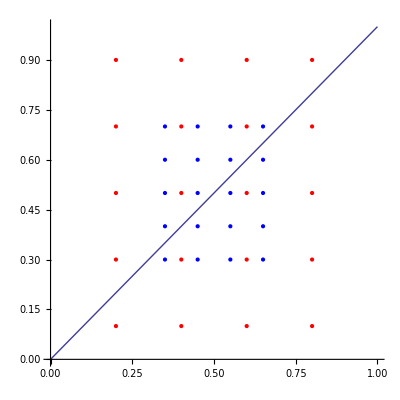

```mathematica
Show[ListPlot[HDCoords, PlotStyle->Red,PlotRange->{{0,1},{0,1}}, AspectRatio->1],ListPlot[LDCoords,PlotStyle->Blue],Plot[y=x,{x,0,1}]]
```

Here are the generated high discriminability stimuli, organized so that their physical location corresponds to the locations in the above graph.

```mathematica
GraphicsGrid[StimuliHD]
```

-Graphics-

And here are the low discriminability stimuli, also spatially organized to correspond to the first graph.

```mathematica
GraphicsGrid[StimuliLD]
```

-Graphics-

Here are the stimuli separated by category (each row is a category). 
  
  High discriminability :

```mathematica
GraphicsRow[HDCatAStims]
GraphicsRow[HDCatBStims]
```

-Graphics-

-Graphics-

Low discriminability :

```mathematica
GraphicsRow[LDCatAStims]
GraphicsRow[LDCatBStims]
```

-Graphics-

-Graphics-